# Mutual Information

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
cd=ColorData[97,"ColorList"];
```

```mathematica
dir ="../AnalysisData/best_categ_pass_agent/";
(*dir = "../AnalysisData/best_offset/";*)
```

## By Subtasks

### Over time

```mathematica
aaO=Import[StringJoin[dir,"mi_size_inT_A_avoid.dat"]];
acO=Import[StringJoin[dir,"mi_size_inT_A_pass.dat"]];
baO=Import[StringJoin[dir,"mi_size_inT_B_avoid.dat"]];
bcO=Import[StringJoin[dir,"mi_size_inT_B_catch.dat"]];
```

```mathematica
max=3.5;
```

"The instantaneous co-fluctuation magnitude between pairs of brain regions.. 
The instantaneous task-relevant information co-fluctuation magnitude between pairs of brain regions..

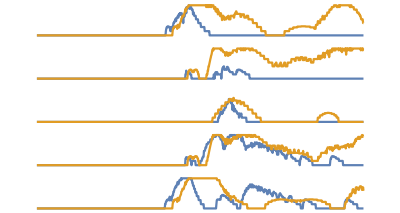

```mathematica
GraphicsColumn[
{
ListLinePlot[{baO[[1]],bcO[[1]]},PlotStyle->{cd[[1]],cd[[2]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[{baO[[2]],bcO[[2]]},PlotStyle->{cd[[1]],cd[[2]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[{baO[[3]],bcO[[3]]},PlotStyle->{cd[[1]],cd[[2]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[{baO[[4]],bcO[[4]]},PlotStyle->{cd[[1]],cd[[2]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[{baO[[5]],bcO[[5]]},PlotStyle->{cd[[1]],cd[[2]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}]
Export["MI_B_subtask_time.eps",%];
```

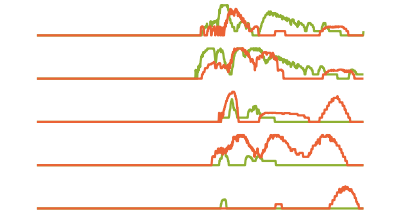

```mathematica
GraphicsColumn[
{
ListLinePlot[{aaO[[1]],acO[[1]]},PlotStyle->{cd[[3]],cd[[4]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[{aaO[[2]],acO[[2]]},PlotStyle->{cd[[3]],cd[[4]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[{aaO[[3]],acO[[3]]},PlotStyle->{cd[[3]],cd[[4]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[{aaO[[4]],acO[[4]]},PlotStyle->{cd[[3]],cd[[4]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[{aaO[[5]],acO[[5]]},PlotStyle->{cd[[3]],cd[[4]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}]
Export["MI_A_subtask_time.eps",%];
```

### Time-averaged

```mathematica
aaT=Flatten[Import[StringJoin[dir,"mi_size_tavg_A_avoid.dat"]]];
acT=Flatten[Import[StringJoin[dir,"mi_size_tavg_A_pass.dat"]]];
baT=Flatten[Import[StringJoin[dir,"mi_size_tavg_B_avoid.dat"]]];
bcT=Flatten[Import[StringJoin[dir,"mi_size_tavg_B_catch.dat"]]];
```

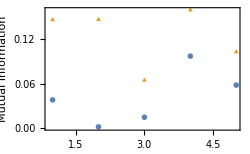

```mathematica
ListPlot[{baT,bcT},PlotRange->All,Frame->True,FrameLabel->{"Neuron","Mutual Information"},ImageSize->250,PlotMarkers->{●,▲}]
Export["MI_B_subtask.eps",%];
```

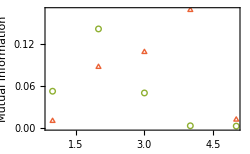

```mathematica
ListPlot[{aaT,acT},PlotStyle->{cd[[3]],cd[[4]]},PlotRange->All,Frame->True,FrameLabel->{"Neuron","Mutual Information"},ImageSize->250,PlotMarkers->{○,△}]
Export["MI_A_subtask.eps",%];
```

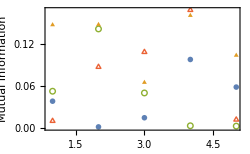

```mathematica
ListPlot[{baT,bcT,aaT,acT},PlotRange->All,Frame->True,FrameLabel->{"Neuron","Mutual Information"},ImageSize->250,PlotMarkers->{●,▲,○,△}]
Export["MI_AB_subtask.eps",%];
```

## By Tasks

### Over time

```mathematica
aO=Import[StringJoin[dir,"mi_size_inT_A_both.dat"]];
bO=Import[StringJoin[dir,"mi_size_inT_B_both.dat"]];
```

```mathematica
max=4.5;
```

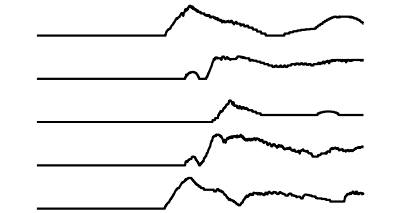

```mathematica
GraphicsColumn[
{
ListLinePlot[bO[[1]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[bO[[2]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[bO[[3]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[bO[[4]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[bO[[5]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}]
Export["MI_B_time.eps",%];
```

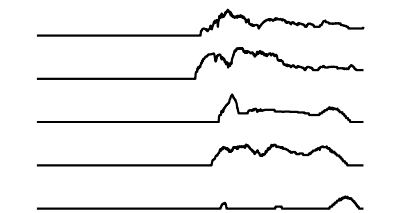

```mathematica
GraphicsColumn[
{
ListLinePlot[aO[[1]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[aO[[2]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[aO[[3]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[aO[[4]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[aO[[5]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}]
Export["MI_A_time.eps",%];
```

### Time-averaged

```mathematica
aT=Flatten[Import[StringJoin[dir,"mi_size_tavg_A_both.dat"]]];
bT=Flatten[Import[StringJoin[dir,"mi_size_tavg_B_both.dat"]]];
```

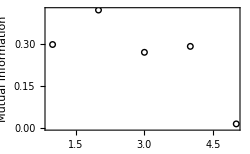

```mathematica
ListPlot[aT,PlotRange->All,Frame->True,FrameLabel->{"Neuron","Mutual Information"},ImageSize->250,PlotStyle->Black,PlotMarkers->{○}]
Export["MI_A.eps",%];
```

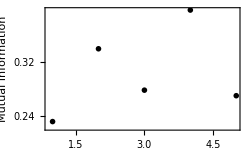

```mathematica
ListPlot[bT,PlotRange->All,Frame->True,FrameLabel->{"Neuron","Mutual Information"},ImageSize->250,PlotStyle->Black,PlotMarkers->{●}]
Export["MI_B.eps",%];
```

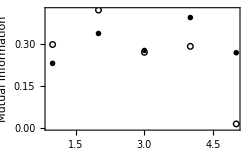

```mathematica
ListPlot[{aT,bT},PlotRange->All,Frame->True,FrameLabel->{"Neuron","Mutual Information"},ImageSize->250,PlotStyle->Black,PlotMarkers->{○,●}]
Export["MI_AB.eps",%];
```

## All data

### Over time

```mathematica
cO=Import[StringJoin[dir,"mi_size_inT_both_both.dat"]];
```

### Time-averaged

```mathematica
cT=Flatten[Import[StringJoin[dir,"mi_size_tavg_both_both.dat"]]];
```

```mathematica
ListPlot[mi1,PlotRange->All,Frame->True,FrameLabel->{"Neuron","Mutual Information"},ImageSize->250,PlotStyle->Black,PlotMarkers->{●}]
```

ListPlot::lpn: mi1 is not a list of numbers or pairs of numbers.

ListPlot[mi1,PlotRange→All,Frame→True,FrameLabel→{Neuron,Mutual Information},ImageSize→250,PlotStyle→GrayLevel[0],PlotMarkers→{●}]